```mathematica
a=.
b=.
c=.
B=.
dt=.
dw=.
v=.
dv=.
q=.
m=.
```

```mathematica
a= v+dv
b=2*dt/dw*dv*v
c=dt/dw*B*v*q/(2*m)
```

dv+v

(2 dt dv v)/dw

(B dt q v)/(2 dw m)

```mathematica
a^2-b
```

-(2 dt dv v)/dw+(dv+v)^2

```mathematica
B=3.1*10^-14
dt=1*10^5
dw=dt/2
v=32.3
dv=3.25*10^-4*v/4
q=1.602*10^-19
m=9.109*10^-31
```

3.1×10^-14

100000

50000

32.3

0.00262438

1.602×10^-19

9.109×10^-31

```mathematica
dvwf0=Sqrt[a^2-b]-a
```

-0.00524875

```mathematica
dvwf1=Sqrt[a^2-b-c*x]-a
```

-32.3026+√(1043.12-0.176099 x)

```mathematica
dvwf=dvwf1-dvwf0
```

-32.2974+√(1043.12-0.176099 x)

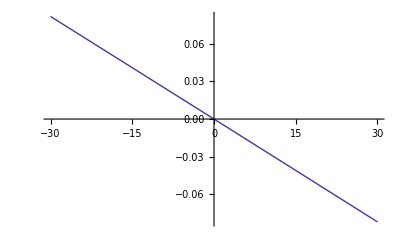

```mathematica
Plot[dvwf,{x,-30,30}]
```

```mathematica
Δt[x_]=dw*(1/(v+dv+dvwf0+dvwf)-1/(v+dv+dvwf0))
```

50000 (-0.0309623+1/(0.+√(1043.12-0.176099 x)))

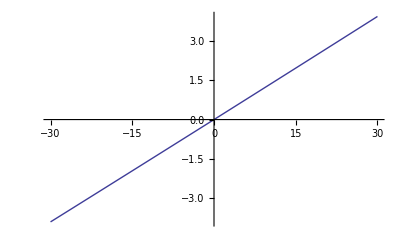

```mathematica
Plot[Δt[x],{x,-30,30}]
```

```mathematica
Δy[θ_]=(dt-dw)/2*Sin[θ]
```

25000 Sin[θ]

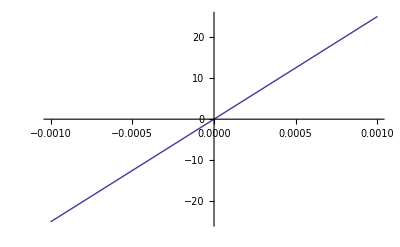

```mathematica
Plot[Δy[θ],{θ,-.001,.001}]
```

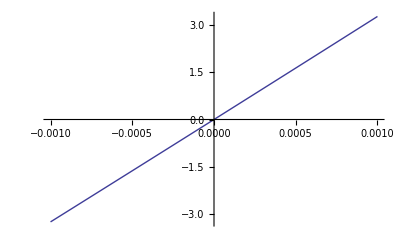

```mathematica
Plot[Δt[Δy[θ]],{θ,-.001,.001}]
```

```mathematica
3.25*10^7/32.5
```

1.×10^6

```mathematica
r=m*v/(q*B)
```

5924.46

```mathematica
(dw/2+Pi*r)/v
```

1350.22

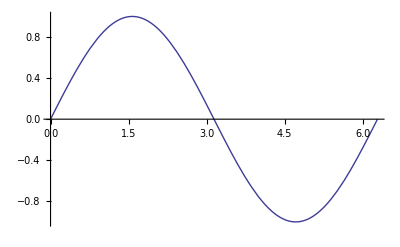

```mathematica
Plot[Sin[x], {x, 0, 2*Pi}]
```

2eV

WolframAlphaQueryResults